```mathematica
ClearAll[GraphPartion`MultipleIsoperimetricVector]
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<10,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
```

{4.44089×10^-16,1.,1.,2.,3.}

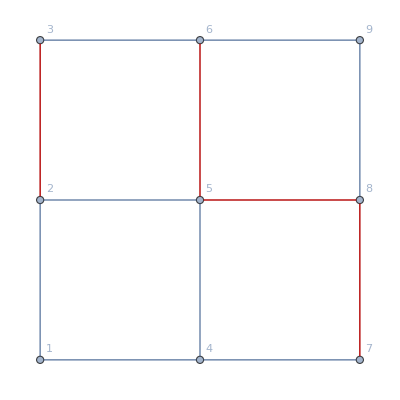
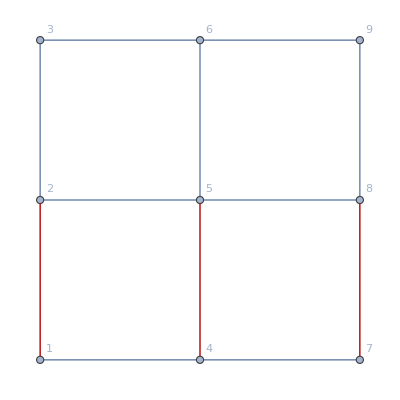
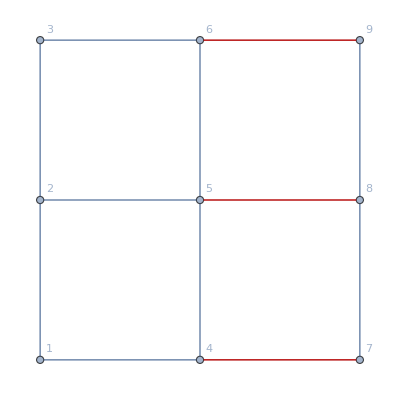
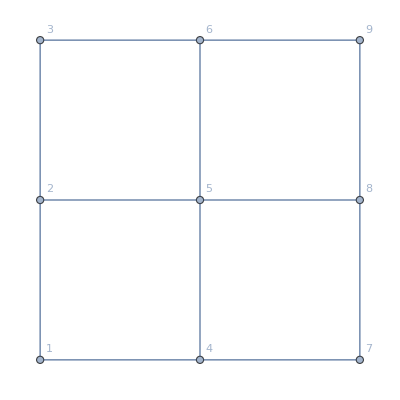
{-Graphics-,-Graphics-,-Graphics-,ShowCuttedEdges[-Graphics-,VectorCut[-Graphics-,VectorPartition[FingerprintVectors[-Graphics-,-Graphics-,Grounds→{}],9,OptimizationOn→True,OptimizationObj→(CriterionPartitionFunction[-Graphics-,#1,0.5]&)],0.5]]}

```mathematica
g= SquareGrid[3];
{ShowSpectralCut[g],ShowIsoperimetricCut[g], ShowMultipleFiedlerCut[g], ShowMultipleIsoperimetricCut[g]}
(*ShowMultipleFiedlerCut[g]*)
(*MultipleIsoperimetricVector[g];*)
```

```mathematica
f :=FingerprintVectors[#1,#2,Grounds->{}]&
f[g,5]
MultipleFiedlerVector[g, NumBasis->5,
			Basis->f]
MultipleIsoperimetricVector[g]
```

{{0.825338,0.634392,0.304341,0.545925,-1.29691},{0.834268,0.258202,0.443985,0.325355,-0.133034},{0.919285,-0.479133,0.601317,0.105855,0.0764631},{0.834268,0.581057,0.125082,0.127963,-0.133034},{0.46061,0.737688,0.604609,0.22977,1.03476},{0.706731,-1.09813,0.936958,-0.208159,0.499376},{0.919285,0.489432,-0.355392,-0.486321,0.0764631},{0.706731,0.516148,-0.657557,-1.19512,0.499376},{0.910362,-0.850515,-1.22904,0.594511,0.557835}}

MultipleFiedlerVector[-Graphics-,NumBasis→5,(FingerprintVectors[#1,#2,Grounds→{}]&)→(FingerprintVectors[#1,#2,Grounds→{}]&)]

MultipleFiedlerVector[-Graphics-,NumBasis→5,(FingerprintVectors[#1,#2,Grounds→{}]&)→(FingerprintVectors[#1,#2,Grounds→OptionValue[MultipleIsoperimetricVector,{},Grounds]]&)]

#### Asymmetric vs. Symmetric

```mathematica
g=LineGraph[GridGraph[{4,4}], VertexLabels->Automatic];
asyms=Table[EdgeDelete[g,EdgeList[g][[RandomSample[Range[Length[EdgeList[g]]],4]]]],20];
asyms =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&/@asyms;

examples=Map[With[{m1=EvaluatePartitionAlg[SpectralAlg, #], m2=EvaluatePartitionAlg[IsoperimetricAlg, #],
m3=EvaluatePartitionAlg[MultipleFiedlerAlg, #], m4 = EvaluatePartitionAlg[MultipleIsoperimetricAlg, #]},
{ShowCuttedEdges[#,m1[[3]]],N[m1[[2]]],
ShowCuttedEdges[#,m2[[3]]],N[m2[[2]]],
ShowCuttedEdges[#,m3[[3]]],N[m3[[2]]],
ShowCuttedEdges[#,m4[[3]]],N[m4[[2]]],
If [m1[[2]]>m3[[2]], "*",Nothing]}]&,asyms];
rowColors = Table[If[examples[[i, -1]]=="*",LightGreen,White] ,{i,1,Length[examples]}];
Grid[Prepend[examples,{"Spectral",Null,"Isoperimetric",Null,"MultipleFiedler",Null,"MultipleIsoperimetric" , Null}], Alignment->Center, Frame->All, Background->{None, Prepend[rowColors,White]}]
```

{-8.88178×10^-15,0.573088,0.605644,1.07708,1.67383}

{-7.10543×10^-15,0.543948,0.624474,0.859445,1.32839}

{-7.10543×10^-15,0.62973,0.690512,1.34816,1.4826}

{-7.99361×10^-15,0.571482,0.652098,1.28375,1.72763}

{-4.44089×10^-15,0.56218,0.605749,1.26007,1.47787}

{-6.21725×10^-15,0.611378,0.675086,1.37248,1.59791}

{-7.10543×10^-15,0.609862,0.62639,1.42155,1.64882}

{-8.88178×10^-15,0.553483,0.66775,1.12657,1.731}

{-9.76996×10^-15,0.612696,0.661652,1.38944,1.49456}

{-8.88178×10^-15,0.620381,0.682371,1.28848,1.77775}

{-6.21725×10^-15,0.501425,0.715786,1.10609,1.65944}

{-8.88178×10^-15,0.521706,0.658363,1.43938,1.73544}

{-3.55271×10^-15,0.319468,0.650662,0.866487,1.72735}

{-6.21725×10^-15,0.560656,0.612609,1.06584,1.34767}

{-7.10543×10^-15,0.594126,0.627202,1.24202,1.55846}

{-7.99361×10^-15,0.509572,0.715297,1.11424,1.66504}

{-7.99361×10^-15,0.561523,0.637145,1.04938,1.41709}

{-6.21725×10^-15,0.603722,0.645383,1.41295,1.6933}

{-4.44089×10^-15,0.582403,0.692241,1.25554,1.65374}

{-7.10543×10^-15,0.593308,0.625544,0.94101,1.37561}